# Deep Quantum Neural Networks

## 1) The Partial Trace Code

This Code is from the Wolfram Library Archive, http://library.wolfram.com/infocenter/MathSource/5571/#downloads

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= Module[{Qubits,TrkM,z,q,n,M,k,p,j,b,i,Permut,c,perm},

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM]
]
```

## 2) Generate Training Data

```mathematica
(*Generate random unitary*)
RG[n_]:=Table[RandomReal[NormalDistribution[0,1]]+I*RandomReal[NormalDistribution[0,1]],{n},{n}];
RU[n_]:=Orthogonalize[RG[n]];
```

```mathematica
(*Define qubit states*)
qubit0={{1},{0}};
qubit1={{0},{1}};
```

```mathematica
qubit0mat=qubit0.ConjugateTranspose[qubit0];
qubit1mat=qubit1.ConjugateTranspose[qubit1];
```

```mathematica
(*Generate a random state*)
MakeState[dim_]:=Module[{tempstate},
tempstate=Table[{RandomReal[NormalDistribution[0,1]]+I*RandomReal[NormalDistribution[0,1]]},{dim}];
tempstate=1/Norm[tempstate] tempstate
]
```

```mathematica
(*Generate a set of random training data*)
MakeTrainingData[N_,dim_,Uni_]:=Module[{TrainingData,i, tempstate},
TrainingData={};
For [i=1,i≤N,i++,
tempstate=MakeState[dim];
TrainingData=Append[TrainingData,{tempstate,Uni.tempstate}];
];
TrainingData
]
```

## 3) The General QNN

### 3.1) Helper functions

```mathematica
(*Generate the channel for layer l in the network*)
MakeLayerChannel[QNNarchitecture_,CurrentUnitaries_,l_,inputstate_]:=Module[{currentstate,tempuni,layerunitary,i1,i2},
currentstate=inputstate;
For[i1=1,i1≤Length[QNNarchitecture⟦l⟧],i1++,
currentstate=KroneckerProduct[currentstate,qubit0mat];
];
tempuni=IdentityMatrix[2^(Length[QNNarchitecture⟦l-1⟧]+Length[QNNarchitecture⟦l⟧])];
For[i2=1,i2≤Length[QNNarchitecture⟦l⟧],i2++,
tempuni=CurrentUnitaries⟦l,i2⟧.tempuni;
];
TraceSystem[tempuni.currentstate.ConjugateTranspose[tempuni],Array[#&,Length[QNNarchitecture⟦l-1⟧]]]
];
```

```mathematica
(*Generate the adjoint channel for layer l in the network*)
MakeAdjointLayerChannel[QNNarchitecture_,CurrentUnitaries_,l_,inputstate_]:=Module[{currentstate,currentstate2,tempuni,i1},
currentstate=KroneckerProduct[IdentityMatrix[2^Length[QNNarchitecture⟦l-1⟧]],inputstate];
currentstate2=qubit0mat;
For[i1=2,i1≤Length[QNNarchitecture⟦l⟧],i1++,
currentstate2=KroneckerProduct[currentstate2,qubit0mat];
];
tempuni=IdentityMatrix[2^(Length[QNNarchitecture⟦l-1⟧]+Length[QNNarchitecture⟦l⟧])];
For[i1=1,i1≤Length[QNNarchitecture⟦l⟧],i1++,
tempuni=CurrentUnitaries⟦l,i1⟧.tempuni;
];
TraceSystem[KroneckerProduct[IdentityMatrix[2^Length[QNNarchitecture⟦l-1⟧]],currentstate2].ConjugateTranspose[tempuni].currentstate.tempuni,Complement[Array[#&,Length[QNNarchitecture⟦l-1⟧]+Length[QNNarchitecture⟦l⟧]],Array[#&,Length[QNNarchitecture⟦l-1⟧]]]]
]
```

```mathematica
(*The feedforward process*)
Feedforward[QNNarchitecture_,TrainingData_,CurrentUnitaries_]:=Module[{storedstates,layerwiselist,currentstate,i1,i2},
storedstates={};
For[i1=1,i1≤Length[TrainingData],i1++,
layerwiselist={};
currentstate=TrainingData⟦i1,1⟧.ConjugateTranspose[TrainingData⟦i1,1⟧];
layerwiselist={currentstate};
For[i2=2,i2≤Length[QNNarchitecture],i2++,
currentstate=MakeLayerChannel[QNNarchitecture,CurrentUnitaries,i2,currentstate];
layerwiselist=Append[layerwiselist,currentstate];
];
storedstates=Append[storedstates,layerwiselist];
];
storedstates
]
```

```mathematica
MakeUpdateMatrix[QNNarchitecture_,λ_,ϵ_,TrainingData_,CurrentUnitaries_,storedstates_,l_,j_]:=Module[{currentqubits,tempstatelist,currentstatelist,tempstate,tempuni,tempstatelist2,sigmalist,tempstate2,tempuni2,firsthalf,secondhalf,i1,i2,i3,i4,i5,i6,b},
(*Make first part of the commutator*)
currentqubits=Length[QNNarchitecture⟦l-1⟧]+Length[QNNarchitecture⟦l⟧];
firsthalf[x_]:=Block[{},
tempstate=storedstates⟦x,l-1⟧;
For[i2=1,i2≤Length[QNNarchitecture⟦l⟧],i2++,
tempstate=KroneckerProduct[tempstate,qubit0mat];
];
tempuni=IdentityMatrix[2^currentqubits];
For[i3=1,i3≤j,i3++,
tempuni=CurrentUnitaries⟦l,i3⟧.tempuni;
];
tempuni.tempstate.ConjugateTranspose[tempuni]
];
(*Make second part of the commutator*)
secondhalf[y_]:=Block[{},
tempstate2=TrainingData⟦y,2⟧.ConjugateTranspose[TrainingData⟦y,2⟧];
For[i5=Length[QNNarchitecture],i5>l,i5--,
tempstate2=MakeAdjointLayerChannel[QNNarchitecture,CurrentUnitaries,i5,tempstate2];
];
tempstate2=KroneckerProduct[IdentityMatrix[2^Length[QNNarchitecture⟦l-1⟧]],tempstate2];
tempuni2=IdentityMatrix[2^currentqubits];
For[i6=j+1,i6≤Length[QNNarchitecture⟦l⟧],i6++,
tempuni2=CurrentUnitaries⟦l,i6⟧.tempuni2;
];
ConjugateTranspose[tempuni2].tempstate2.tempuni2
];
(*Make exponential parameter matrix*)
MatrixExp[-2^Length[QNNarchitecture⟦l-1⟧] ϵ/(λ Length[TrainingData])*Sum[TraceSystem[
firsthalf[b].secondhalf[b]-secondhalf[b].firsthalf[b]
,Complement[Array[#&,currentqubits],Array[#&,Length[QNNarchitecture⟦l-1⟧]],{j+Length[QNNarchitecture⟦l-1⟧]}]
]
,{b,1,Length[TrainingData]}
]
]
]
```

```mathematica
MakeSwapMatrix[numberofqubits_,swapqubit1_,swapqubit2_]:=Module[{qubitarray,savearray,swappedqubitarray,basis,swappedbasis},
qubitarray=Array[Subscript[a, #]&,{numberofqubits}];
basis=Flatten[Table[KroneckerProduct@@qubitarray,Evaluate[Sequence@@({#,{qubit0,qubit1}}&/@qubitarray)]],numberofqubits-1];
savearray=qubitarray;
{qubitarray⟦swapqubit1⟧,qubitarray⟦swapqubit2⟧}={qubitarray⟦swapqubit2⟧,qubitarray⟦swapqubit1⟧};
swappedqubitarray=qubitarray;
swappedbasis=Flatten[Table[KroneckerProduct@@swappedqubitarray,Evaluate[Sequence@@({#,{qubit0,qubit1}}&/@savearray)]],numberofqubits-1];
Table[(ConjugateTranspose[basis⟦i⟧].swappedbasis⟦j⟧)⟦1,1⟧,{i,1,Length[basis]},{j,1,Length[basis]}]
]
```

### 3.2) Training the QNN

```mathematica
(*The cost function*)
CostFunction[TrainingData_,outputstates_]:=Module[{i},
1/Length@TrainingData Sum[ConjugateTranspose[TrainingData⟦i,2⟧].outputstates⟦i⟧.TrainingData⟦i,2⟧,{i,1,Length@TrainingData}]
]
```

```mathematica
(*Input to the training function: QNNarchitecture in the form {{1,1},{2,2}} for a 2-2 network, e.g., parameters λ and ϵ, the set of training data, the list of initial unitaries (with the empty list {} for the input layer),and the number of training rounds.*)
QNNTraining[QNNarchitecture_,λ_,ϵ_,TrainingData_,InitialUnitaries_,TrainingRounds_]:=Module[{s=0,currentunitaries,layerwiseoutput,plotlist,currentqubits,k,i1,i2},
currentunitaries=InitialUnitaries;
layerwiseoutput=Feedforward[QNNarchitecture,TrainingData,currentunitaries];
plotlist={{s,Chop[CostFunction[TrainingData,layerwiseoutput⟦;;,-1⟧]]⟦1,1⟧}};
For[k=1,k≤TrainingRounds,k++,(*Loop over training rounds*)
For[i1=2,i1≤Length[QNNarchitecture],i1++,(*Loop over the layers in the QNN*)
currentqubits=Length[QNNarchitecture⟦i1-1⟧]+Length[QNNarchitecture⟦i1⟧];
For[i2=1,i2≤Length[QNNarchitecture⟦i1⟧],i2++,(*Loop over the perceptrons in layer i2*)
currentunitaries⟦i1,i2⟧=MakeSwapMatrix[currentqubits,i2+Length[QNNarchitecture⟦i1-1⟧],1+Length[QNNarchitecture⟦i1-1⟧]].KroneckerProduct[MakeUpdateMatrix[QNNarchitecture,λ,ϵ,TrainingData,currentunitaries,layerwiseoutput,i1,i2],IdentityMatrix[2^(Length[QNNarchitecture⟦i1⟧]-1)]].MakeSwapMatrix[currentqubits,i2+Length[QNNarchitecture⟦i1-1⟧],1+Length[QNNarchitecture⟦i1-1⟧]].currentunitaries⟦i1,i2⟧;
];
];
s=s+ϵ;
layerwiseoutput=Feedforward[QNNarchitecture,TrainingData,currentunitaries];
plotlist=Append[plotlist,{s,Chop[CostFunction[TrainingData,layerwiseoutput⟦;;,-1⟧]]⟦1,1⟧}];
];
{plotlist,currentunitaries}
]
```

### 3.3) Tests

```mathematica
RandomUni=RU[4];
TestTrainingData=MakeTrainingData[10,4,RandomUni];
```

```mathematica
ExampleQNNarchitecture={{1,1},{2,2,2},{3,3}};
```

```mathematica
TestInitialUnis={{},{KroneckerProduct[RU[8],IdentityMatrix[2^2]],
MakeSwapMatrix[5,3,4].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,4],MakeSwapMatrix[5,3,5].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,5]},{KroneckerProduct[RU[16],IdentityMatrix[2]],MakeSwapMatrix[5,4,5].KroneckerProduct[RU[16],IdentityMatrix[2]].MakeSwapMatrix[5,4,5]}};
```

```mathematica
plotliste=QNNTraining[ExampleQNNarchitecture,1,0.1,TestTrainingData,TestInitialUnis,500]⟦1⟧;
```

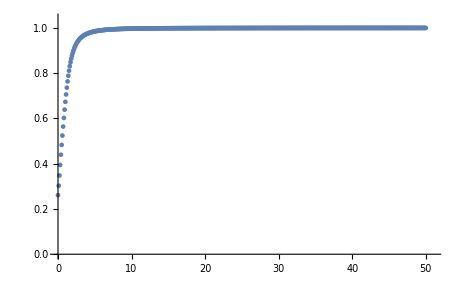

```mathematica
ListPlot[plotliste,PlotRange->{{0,51},{0,1.04}}]
```

```mathematica
ExampleQNNarchitecture2={{1,1},{2,2}};
```

```mathematica
TestInitialUnis2={{},{KroneckerProduct[RU[8],IdentityMatrix[2]],
MakeSwapMatrix[4,3,4].KroneckerProduct[RU[8],IdentityMatrix[2]].MakeSwapMatrix[4,3,4]}};
```

```mathematica
plotlist1a=QNNTraining[ExampleQNNarchitecture2,2,0.1,TestTrainingData,TestInitialUnis2,200]⟦1⟧;
plotlist1b=QNNTraining[ExampleQNNarchitecture2,1,0.1,TestTrainingData,TestInitialUnis2,200]⟦1⟧;
plotlist1c=QNNTraining[ExampleQNNarchitecture2,0.5,0.1,TestTrainingData,TestInitialUnis2,200]⟦1⟧;
```

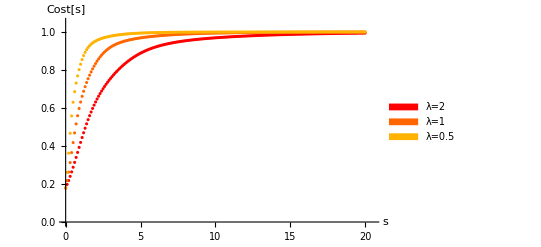

```mathematica
plot1=ListPlot[{plotlist1a,plotlist1b,plotlist1c},PlotRange->{{0,20.5},{0,1.05}},AxesOrigin->{0,0},AxesLabel->{"s","Cost[s]"},PlotStyle->{RGBColor[1,0.0,0],RGBColor[1,0.4,0],RGBColor[1,0.7,0]},LabelStyle->Large,PlotLegends->SwatchLegend[{RGBColor[1,0.0,0],RGBColor[1,0.4,0],RGBColor[1,0.7,0]},{"λ=2","λ=1","λ=0.5"}]]
```

## 4) Tasks

### 4.1) Generalisation

```mathematica
(*Formula for estimate of cost function*)
boundRand[n_,N_,D_]:=n/N+(N-n)/(N D (D+1)) (D+Min[n^2+1,D^2]);
```

```mathematica
AverageCost[n_,QNNarchitecture_,ϵ_,λ_,DataSet_,IntitialUnitaries_,steps_,rounds_]:=Module[{TrainingSet,TestSet,Costpoints,i=1,LearnedUnitaries},
Costpoints={};
Monitor[
While[i≤rounds,
TrainingSet=RandomSample[DataSet,n];
TestSet=DataSet;
LearnedUnitaries=QNNTraining[QNNarchitecture,λ,ϵ,TrainingSet,IntitialUnitaries,steps]⟦2⟧;
Costpoints=Append[Costpoints,CostFunction[TestSet,Feedforward[QNNarchitecture,TestSet,LearnedUnitaries]⟦;;,-1⟧]];
i++;
];
,i];
1/Length[Costpoints]*Total[Costpoints]
]
```

#### 4.1.1) D = 4

```mathematica
BoundPlotPointsD4=boundRand[#,10,4]&/@{1,2,3,4}//N
```

{0.37,0.56,0.79,1.}

```mathematica
ExampleQNNarchitecture2={{1,1},{2,2}};
```

```mathematica
TestInitialUnis2={{},{KroneckerProduct[RU[8],IdentityMatrix[2]],
MakeSwapMatrix[4,3,4].KroneckerProduct[RU[8],IdentityMatrix[2]].MakeSwapMatrix[4,3,4]}};
```

```mathematica
Uni4=RU[4];
```

```mathematica
TestSet4=MakeTrainingData[10,4,Uni4];
```

```mathematica
PlotforGenTaskD4={#,AverageCost[#,ExampleQNNarchitecture2,0.1,1.5,TestSet4,TestInitialUnis2,1000,20]⟦1,1⟧}&/@{1,2,3,4}
```

{{1,0.398699+1.5542×10^-18 ⅈ},{2,0.559709-8.63432×10^-19 ⅈ},{3,0.739731+1.21363×10^-18 ⅈ},{4,0.966294+1.66181×10^-18 ⅈ}}

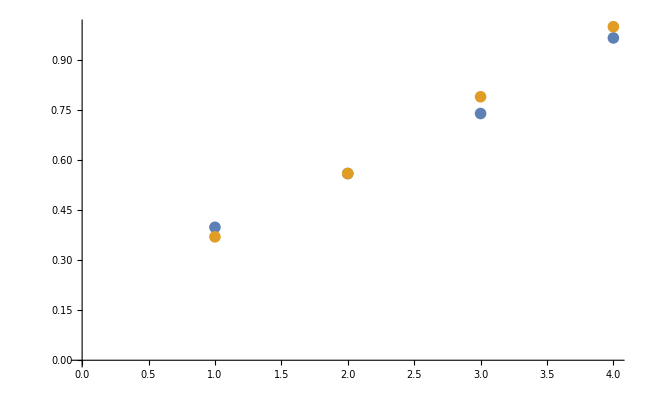

```mathematica
ListPlot[{PlotforGenTaskD4,BoundPlotPointsD4}]
```

#### 4.1.2) D = 8

```mathematica
BoundPlotPointsD8=boundRand[#,10,8]&/@{1,2,3,4,5,6,7,8}//N
```

{0.225,0.344444,0.475,0.608333,0.736111,0.85,0.941667,1.}

```mathematica
Uni8=RU[8];
```

```mathematica
TestSet333=MakeTrainingData[10,8,Uni8];
```

```mathematica
Networkarchitecture333={{1,1,1},{2,2,2},{3,3,3}};
```

```mathematica
TestInitialUnis333={{},{KroneckerProduct[RU[16],IdentityMatrix[2^2]],
MakeSwapMatrix[6,4,5].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,4,5],MakeSwapMatrix[6,4,6].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,4,6]},{KroneckerProduct[RU[16],IdentityMatrix[2^2]],
MakeSwapMatrix[6,4,5].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,4,5],MakeSwapMatrix[6,4,6].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,4,6]}};
```

```mathematica
PlotforGenTaskD8={#,AverageCost[#,ExampleQNNarchitecture6,0.1,1.5,TestSet8,TestInitialUnis6,1000,20]⟦1,1⟧}&/@{1,2,3,4,5,6,7,8}
```

{{1,0.220197+1.52452×10^-18 ⅈ},{2,0.344566-1.39537×10^-18 ⅈ},{3,0.467219+4.17282×10^-18 ⅈ},{4,0.615367-1.73838×10^-18 ⅈ},{5,0.739379-2.16339×10^-18 ⅈ},{6,0.856904+1.50528×10^-18 ⅈ},{7,0.948124-6.89959×10^-19 ⅈ},{8,0.985477+2.89319×10^-18 ⅈ}}

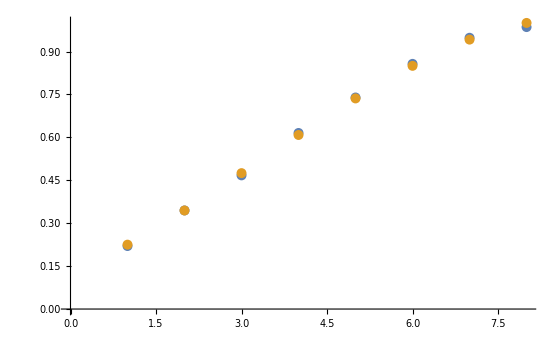

```mathematica
ListPlot[{PlotforGenTaskD8,BoundPlotPointsD8}]
```

### 4.2) Robustness to noisy data

```mathematica
DataSet[N_,dim_]:=Module[{RandomMatrix,data,i,tempstate},
RandomMatrix=RU[dim];
data={};
For[i=1,i≤N,i++,
tempstate=MakeState[dim];
data=Append[data,{tempstate,RandomMatrix.tempstate}];
];
data
]
```

```mathematica
TestDataSet=DataSet[100,4];
```

```mathematica
TestNoisySet=Table[{MakeState[4],MakeState[4]},{i,1,100}];
```

```mathematica
MakePlotData[TestDataSet_,NoisyDataSet_,QNNarchitecture_,InitialUnitaries_,TrainingRounds_,ϵ_,λ_,numberofdata_,stepsize_]:=Module[{NoisyDataPlot,i=0,TestSet,QNNoutput,OutputState},
NoisyDataPlot={};
Monitor[While[i≤numberofdata,
TestSet=Join[RandomSample [TestDataSet,numberofdata-i],RandomSample[NoisyDataSet,i]];
QNNoutput=QNNTraining[QNNarchitecture,λ,ϵ,TestSet,InitialUnitaries,TrainingRounds];
OutputState=Feedforward[QNNarchitecture,TestDataSet,QNNoutput⟦2⟧];
NoisyDataPlot=Append[NoisyDataPlot,{i,CostFunction[TestDataSet,OutputState⟦;;,-1⟧]⟦1,1⟧//Chop}];
i=i+stepsize;
];,
i];
NoisyDataPlot
]
```

#### 4.2.1) 2-3-2 network

```mathematica
ExampleQNNarchitecture={{1,1},{2,2,2},{3,3}};
```

```mathematica
TestInitialUnis={{},{KroneckerProduct[RU[8],IdentityMatrix[2^2]],
MakeSwapMatrix[5,3,4].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,4],MakeSwapMatrix[5,3,5].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,5]},{KroneckerProduct[RU[16],IdentityMatrix[2]],MakeSwapMatrix[5,4,5].KroneckerProduct[RU[16],IdentityMatrix[2]].MakeSwapMatrix[5,4,5]}};
```

```mathematica
noisydata=MakePlotData[TestDataSet,TestNoisySet,ExampleQNNarchitecture,TestInitialUnis,300,0.1,1,100,5];
```

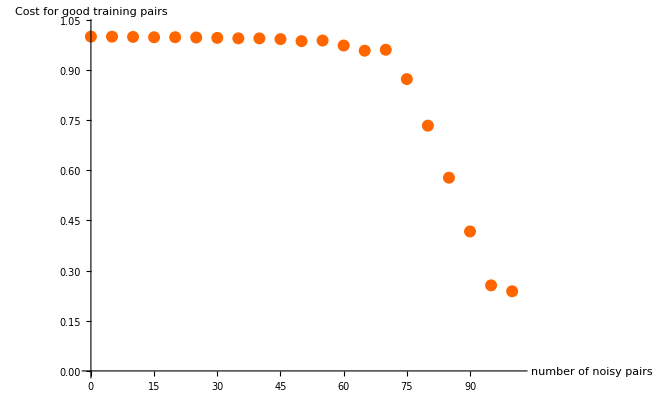

```mathematica
verynoisyplot=ListPlot[noisydata,PlotRange->{{0,101.5},{0,1.03}},AxesOrigin->{0,0},AxesLabel->{"number of noisy pairs","Cost for good training pairs"},PlotStyle->{RGBColor[1,0.4,0]}]
```

#### 4.2.2) 2-2 network

```mathematica
QNNarch22={{1,1},{2,2}};
InitialUnitaries22={{},{KroneckerProduct[RU[8],IdentityMatrix[2]],
MakeSwapMatrix[4,3,4].KroneckerProduct[RU[8],IdentityMatrix[2]].MakeSwapMatrix[4,3,4]}};
```

```mathematica
noisydata22=MakePlotData[TestDataSet,TestNoisySet,QNNarch22,InitialUnitaries22,500,0.1,1,100,5];
```

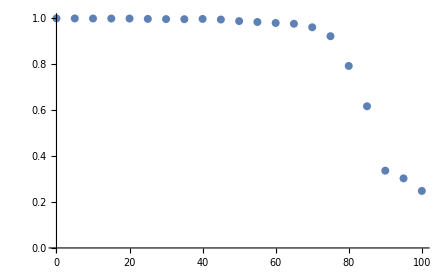

```mathematica
ListPlot[noisydata22]
```

### 4.3) Big Networks

```mathematica
RandomUni=RU[4];
TestTrainingData=MakeTrainingData[5,4,RandomUni];
```

```mathematica
Networkarchitecture2332={{1,1},{2,2,2},{3,3,3},{4,4}};
```

```mathematica
TestInitialUnis2332={{},{KroneckerProduct[RU[8],IdentityMatrix[2^2]],
MakeSwapMatrix[5,3,4].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,4],MakeSwapMatrix[5,3,5].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,5]},{KroneckerProduct[RU[16],IdentityMatrix[2^2]],
MakeSwapMatrix[6,5,4].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,5,4],MakeSwapMatrix[6,6,4].KroneckerProduct[RU[16],IdentityMatrix[2^2]].MakeSwapMatrix[6,6,4]},{KroneckerProduct[RU[16],IdentityMatrix[2]],
MakeSwapMatrix[5,5,4].KroneckerProduct[RU[16],IdentityMatrix[2]].MakeSwapMatrix[5,5,4]}};
```

```mathematica
plotlist2332three=QNNTraining[Networkarchitecture2332,3,0.1,TestTrainingData,TestInitialUnis2332,1000]⟦1⟧;
```

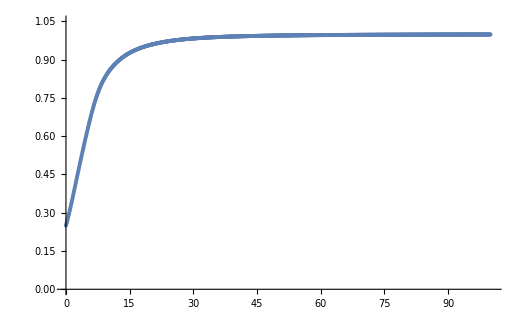

```mathematica
ListPlot[plotlist2332three,PlotRange->{{0,100.5},{0,1.05}}]
```

```mathematica
Networkarchitecture23432={{1,1},{2,2,2},{3,3,3,3},{4,4,4},{5,5}};
```

```mathematica
TestInitialUnis23432={{},{KroneckerProduct[RU[8],IdentityMatrix[2^2]],
MakeSwapMatrix[5,3,4].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,4],MakeSwapMatrix[5,3,5].KroneckerProduct[RU[8],IdentityMatrix[2^2]].MakeSwapMatrix[5,3,5]},
{KroneckerProduct[RU[16],IdentityMatrix[2^3]],
MakeSwapMatrix[7,5,4].KroneckerProduct[RU[16],IdentityMatrix[2^3]].MakeSwapMatrix[7,5,4],MakeSwapMatrix[7,6,4].KroneckerProduct[RU[16],IdentityMatrix[2^3]].MakeSwapMatrix[7,6,4],MakeSwapMatrix[7,7,4].KroneckerProduct[RU[16],IdentityMatrix[2^3]].MakeSwapMatrix[7,7,4]},{KroneckerProduct[RU[32],IdentityMatrix[2^2]],MakeSwapMatrix[7,5,6].KroneckerProduct[RU[32],IdentityMatrix[2^2]].MakeSwapMatrix[7,5,6],MakeSwapMatrix[7,5,7].KroneckerProduct[RU[32],IdentityMatrix[2^2]].MakeSwapMatrix[7,5,7]},{KroneckerProduct[RU[16],IdentityMatrix[2]],
MakeSwapMatrix[5,5,4].KroneckerProduct[RU[16],IdentityMatrix[2]].MakeSwapMatrix[5,5,4]}};
```

```mathematica
plotlist23432two=QNNTraining[Networkarchitecture23432,4,0.1,TestTrainingData,TestInitialUnis23432,1000]⟦1⟧;
```

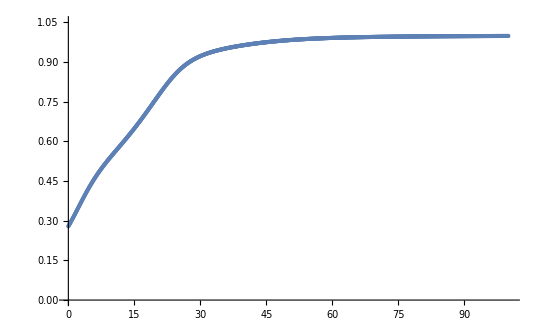

```mathematica
ListPlot[plotlist23432two,PlotRange->{{0,100.5},{0,1.05}}]
```